```mathematica
tick[x_]:=(1+Cos[π x])/x
```

```mathematica
tick[n_]:=(1+Cos[π n])/n
```

```mathematica
even[n_]:=n/2
```

```mathematica
odd[n_]:=3n+1
```

```mathematica
tock[n_]:=1-tick[n]
```

```mathematica
tick[n]
```

(1+Cos[n π])/n

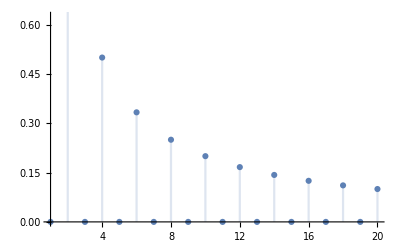

```mathematica
DiscretePlot[(1+Cos[n π])/n,{n,1,20}]
```

```mathematica
tick[n_]:=(1+Cos[π n])/2
```

```mathematica
tock[n]
```

1+1/2 (-1-Cos[n π])

```mathematica
tick[n]
```

1/2 (1+Cos[n π])

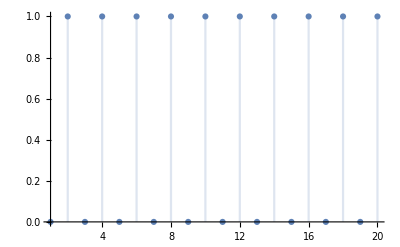

```mathematica
DiscretePlot[1/2 (1+Cos[n π]),{n,1,20}]
```

```mathematica
tick[n]even[n]+tock[n]odd[n]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

```mathematica
col[n_]:=tick[n]even[n]+tock[n]odd[n]
```

```mathematica
col[n]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

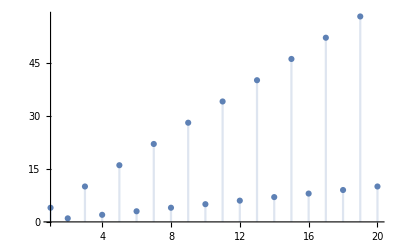

```mathematica
DiscretePlot[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]),{n,1,20}]
```

```mathematica
col[10]
```

5

```mathematica
col[11]
```

34

```mathematica
Nest[col,n,2]
```

(1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])

```mathematica
Nest[col,n,1]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

```mathematica
Nest[col,n,0]
```

n

```mathematica
FullSimplify[Nest[col,n,2],n∈]
```

1/16 (22+49 n-7 (-1)^n (2+5 n)+(-18-35 n+5 (-1)^n (2+5 n)) Sin[1/4 (-7 n+(-1)^n (2+5 n)) π])

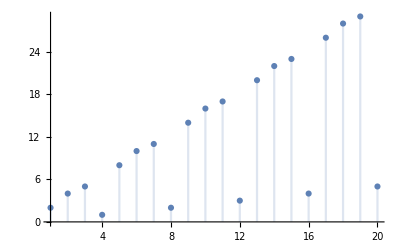

```mathematica
DiscretePlot[1/16 (22+49 n-7 (-1)^n (2+5 n)+(-18-35 n+5 (-1)^n (2+5 n)) Sin[1/4 (-7 n+(-1)^n (2+5 n)) π]),{n,1,20}]
```

```mathematica
TrigToExp[1/16 (22+49 n-7 (-1)^n (2+5 n)+(-18-35 n+5 (-1)^n (2+5 n)) Sin[1/4 (-7 n+(-1)^n (2+5 n)) π])]
```

1/16 (22+49 n-7 (-1)^n (2+5 n)+1/2 ⅈ (ⅇ^(-1/4 ⅈ (-7 n+(-1)^n (2+5 n)) π)-ⅇ^(1/4 ⅈ (-7 n+(-1)^n (2+5 n)) π)) (-18-35 n+5 (-1)^n (2+5 n)))

```mathematica
DiscretePlot[1/16 (22+49 n-7 (-1)^n (2+5 n)+1/2 ⅈ (ⅇ^(-1/4 ⅈ (-7 n+(-1)^n (2+5 n)) π)-ⅇ^(1/4 ⅈ (-7 n+(-1)^n (2+5 n)) π)) (-18-35 n+5 (-1)^n (2+5 n))),{n,1,20}]
```

-Graphics-

```mathematica
TrigReduce[1/16 (22+49 n-7 (-1)^n (2+5 n)+(-18-35 n+5 (-1)^n (2+5 n)) Sin[1/4 (-7 n+(-1)^n (2+5 n)) π])]
```

1/16 (22-14 (-1)^n+49 n-35 (-1)^n n-18 Sin[1/4 (-7 n+(-1)^n (2+5 n)) π]+10 (-1)^n Sin[1/4 (-7 n+(-1)^n (2+5 n)) π]-35 n Sin[1/4 (-7 n+(-1)^n (2+5 n)) π]+25 (-1)^n n Sin[1/4 (-7 n+(-1)^n (2+5 n)) π])

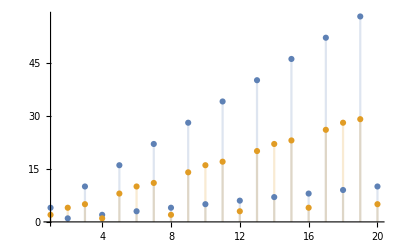

```mathematica
DiscretePlot[{
col[n],1/16 (22+49 n-7 (-1)^n (2+5 n)+(-18-35 n+5 (-1)^n (2+5 n)) Sin[1/4 (-7 n+(-1)^n (2+5 n)) π])
},{n,1,20}]
```

```mathematica
NestList[col,n,5]
```

{n,4,(1+3 ((1+3 (1+1)) (1+1)+1)) (1+1/2 1)+1/4 1 (1+1)}
 |  |  |  |

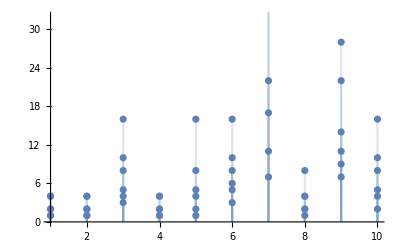

```mathematica
DiscretePlot[
Out[27]
,{n,1,10}]
```

```mathematica
col[n]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

```mathematica
col[12]
```

6

```mathematica
Table[Nest[col,12,i],{x,1,10,1}]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[col,12,i].

{Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i],Nest[col,12,i]}

```mathematica
Table[Nest[col,12,i],{i,1,10,1}]
```

{6,3,10,5,16,8,4,2,1,4}

```mathematica
Table[Nest[col,12,i],{i,1,15,1}]
```

{6,3,10,5,16,8,4,2,1,4,2,1,4,2,1}

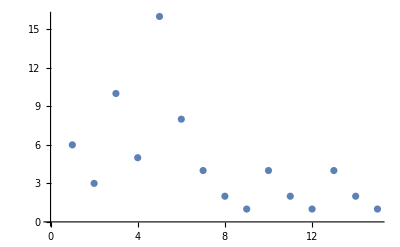

```mathematica
ListPlot[{6,3,10,5,16,8,4,2,1,4,2,1,4,2,1}]
```

```mathematica
Table[Nest[col,12,i],{i,1,20,1}]
```

{6,3,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

```mathematica
Table[Nest[col,19,i],{i,1,20,1}]
```

{58,29,88,44,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

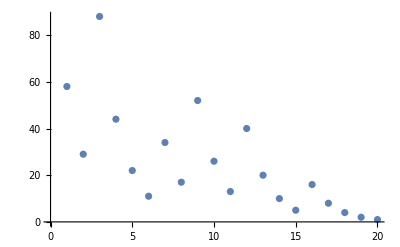

```mathematica
ListPlot[{58,29,88,44,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}]
```

```mathematica
Table[Nest[col,27,i],{i,1,111,1}]
```

{82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

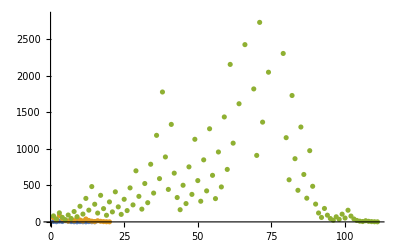

```mathematica
ListPlot[{
Table[Nest[col,12,i],{i,1,15,1}],
Table[Nest[col,19,i],{i,1,20,1}],
Table[Nest[col,27,i],{i,1,111,1}]
}]
```

```mathematica
colcount[n_]:=Piecewise[{{1, n==1}, {colcount[col[n]], n>1}}]
```

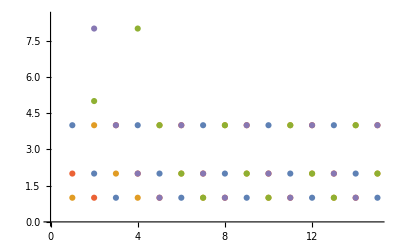

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,15,1}],{k,1,5}]
]
```

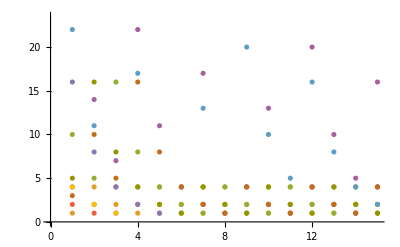

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,15,1}],{k,1,10}]
]
```

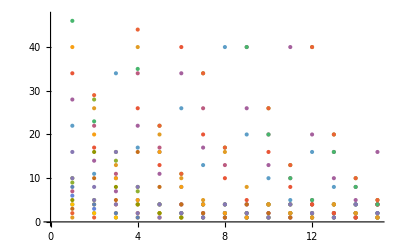

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,15,1}],{k,1,20}]
]
```

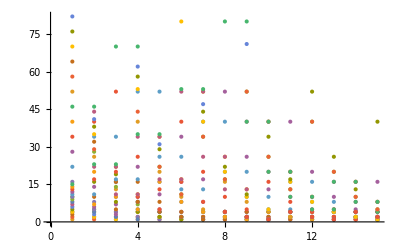

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,15,1}],{k,1,30}]
]
```

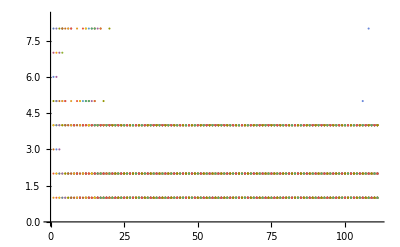

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,111,1}],{k,1,30}]
]
```

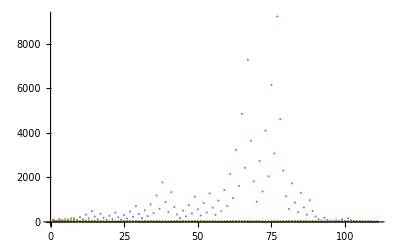

```mathematica
ListPlot[
Table[Table[Nest[col,k,i],{i,1,111,1}],{k,1,30}]
,PlotRange->Full]
```